0.+8.98755×10^16 Cos[(N1 π)/2000]^2-8.98755×10^16 Cos[((1+N1) π)/2000]^2

0.-8.98755×10^16 Sin[(N1 π)/2000]^2+8.98755×10^16 Sin[((1+N1) π)/2000]^2

0.+1.12863×10^26 Cos[(N1 π)/2000]^3-1.12863×10^26 Cos[((1+N1) π)/2000]^3

0.-1.12863×10^26 Sin[(N1 π)/2000]^3+1.12863×10^26 Sin[((1+N1) π)/2000]^3

2.99792×10^8

1000

-Graphics-

-Graphics-

c^2 = fourSpaceVolume / twoSpaceArea = 1 / (u0 F0)

u0 fourSpaceVolume = twoSpaceArea / F0

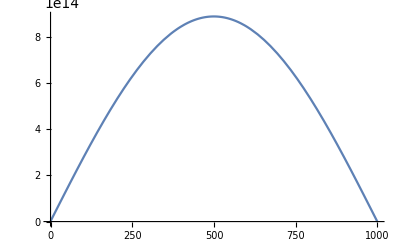

-Graphics-

-Graphics-

-Graphics-

```mathematica
Expand[(R^2 - (R - dR)^2)]
Expand[((X + dX)^2 - X^2)]
Expand[(4/3 Pi R^3 - 4/3 Pi(R - dR)^3)]
Expand[(4/3 Pi(X + dX)^3 - 4/3 Pi X^3)]
c = 2.99792458*10^8
n3 = 1000
Plot[{((Pi R^2 - Pi(R - dR)^2)+ (Pi(X + dX)^2- Pi X^2))* c^2-((Pi R^4 - Pi(R - dR)^4)+ (Pi(X + dX)^4- Pi X^4))}, {N1, 0, n}]
Plot[{((Pi R^2 - Pi(R - dR)^2))* 2 c^2-((Pi R^4 - Pi(R - dR)^4)+ (Pi(X + dX)^4- Pi X^4))}, {N1, 0, n}]
Print["4 d sphere hypervolume = (1/2) Pi^2"]
Print["2 d area = Pi"] 
Print["c^2 = dfourSpaceVolume / dtwoSpaceArea = 1 / (u0 F0)"]
Print["u0 dfourSpaceVolume = dtwoSpaceArea / F0"]
Print["c^2 = (1/2) Pi^2 dfourSpaceVolume / Pi dtwoSpaceArea = (Pi/2)c^2 = (Pi/2) / (u0 F0)"]
Print["u0 dfourSpaceVolume  = Pi/2 dtwoSpaceArea / F0"]
Plot[{((Pi R^2 - Pi(R - dR)^2)+ (Pi(X + dX)^2- Pi X^2))}, {N1, 0, n}]
Plot[{((Pi R^4 - Pi(R - dR)^4)+ (Pi(X + dX)^4- Pi X^4))}, {N1, 0, n}]
Plot[{(Pi R^4 - Pi(R - dR)^4)}, {N1, 0, n}]
Plot[{((Pi(X + dX)^4- Pi X^4))}, {N1, 0, n}]
```